# Numerical Diagonalisation of an arbitrary* Hamiltonian

```mathematica
(* confirm output is correct eigenstate? Maybe solve T.I schrod (with energy of each), access interpoators at grid points and compare list *)
```

## Initialisation

```mathematica
ClearAll["Global`*"]
```

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< EigenFunctions`
<< PlotFunctions`
```

## Testing Accuracy

Remember that the smaller the energy eigenvalue, the slower the eigenfunction’s phase will evolve in time!

```mathematica
(*
solveEvolution::usage = "returns an interpolator of the spacetime evolution of a continuous wavefunction";

solveEvolution[psi_, potential_, {xL_, xR_}, duration_:1] :=
	NDSolveValue[
		{
			ⅈ ψ^(0,1)[x, t] ==  -ψ^(2,0)[x, t] / 2 + ψ[x, t] potential[x],
			ψ[x, 0] == psi[x],
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, 
		{x, xL, xR},
		{t, 0, duration}
	];

solveDiscreteEvolution::usage = "returns an interpolator of the spacetime evolution a discrete wavefunction";
				
solveDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	Module[
		{xL, xR, psi, ϕclone, potential, evol},
		xL = grid[[1]];
		xR = grid[[-1]];
		
		(* enforce boundary conditions *)
		ϕclone = ϕlist;
		
		(*
		ϕclone[[1]] = ϕclone[[-1]] = 0;
		*)
	
			
		(* build continuous functions for evolution *)
		psi = ListInterpolation[ϕclone, {{xL, xR}}, Method -> "Spline"];
		potential = ListInterpolation[Vlist, {{xL, xR}}, Method -> "Spline"]; 
		solveEvolution[psi, potential, {xL, xR}, duration]
	]
	
animateDiscreteEvolution::usage = "returns an animation of the spacetime evolution of a discrete wavefunction";
		
animateDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{evol},
		evol = solveDiscreteEvolution[ϕlist, Vlist, {grid[[1]], grid[[-1]]}, duration];
		Animate[
			plotContinuousψ[evol[x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration}
		]
	]
	
animateEigensystemEvolutionNEW[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{solutions},
		solutions[n_] := 
			solutions[n] = solveDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			plotContinuousψ[solutions[n][x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration},
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
	
animateEigensystemEvolution[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{animFunc},
		animFunc[n_] := 
			animFunc[n] = animateDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			animFunc[n],
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
*)
```

```mathematica
(*
animateSpectrum[{x_, xL_, xR_, Δx_}, V_, numModes_:4, duration_:1] :=
	DynamicModule[
		{grid, potential, eigfuncs, eigvals},
			
		grid = Range[xL, xR, Δx];
		potential = If[
			V === 0,
			ConstantArray[0, Length[grid]],
			(V /. x -> #1 &) @ grid
		];
		
		(* add very high potential to end-points to improve stability; finite differences :'c  *)
		potential[[1]] = potential[[-1]] = 10^4;
		
		{eigvals, eigfuncs} = getEigenmodes[potential, grid, numModes];
		animateEigensystemEvolutionNEW[{eigvals, eigfuncs}, potential, grid, duration]
]
*)
```

# Testing new Simulations Paclet

```mathematica
schrodEqu[V_, r__, t_] :=
	 ⅈ D[ψ[r, t], t] ==  - Laplacian[ψ[r, t], {r}] / 2 + ψ[r, t] V[r]
```

```mathematica
schrodEqu[(1/2#^2&), x, y, t]
```

ⅈ ψ^(0,0,1)[x,y,t]==1/2 x^2 ψ[x,y,t]+1/2 (-ψ^(0,2,0)[x,y,t]-ψ^(2,0,0)[x,y,t])

```mathematica
NDSolveValue[
		{
			schrodEqu[1/2#^2&, x, t],
			ψ[x, 0] == 1/(√2)1/π^(1/4)Exp[-x^2/2] HermiteH[1, x] ,
			ψ[-5,  t] == 0,
			ψ[5,t] == 0    
		},
		ψ, 
		{t, 0, 1},
		{x} ∈ Interval[{-5,5}]
	]
```

InterpolatingFunction[{{-5., 5.}, {0., 1.}}, <>]

```mathematica
thing = 	NDSolveValue[
		{
			schrodEqu[1/2#^2&, x, y, t],
			ψ[x, y, 0] == 1/(√2)1/π^(1/4)Exp[-x^2/2] Exp[-y^2/2] HermiteH[1, x]  HermiteH[1,y] Exp[ⅈ x^2+ⅈ y^2],
		(*
		ψ[-5, y,  t] == 0,
			ψ[5, y, t] == 0,    (* apparently x0, y0 can be infinity! *) 
		ψ[x, -5, t] == 0,
		ψ[x, 5, t] == 0
		*)
		DirichletCondition[ψ[x, y, t] == 0,True]
		},
		ψ, 
		{t, 0, 5},
		{x, y} ∈ Rectangle[{-5,-5},{5,5}],
		Method -> {"EquationSimplification" -> "MassMatrix"}
	]
```

InterpolatingFunction[{{-5., 5.}, {-5., 5.}, {0., 5.}}, <>]

```mathematica
intervalfunctest[func_, Element[vars_, domain_]] :=
	If [
		Length[vars] ≤ 1,
		Plot[func, vars ∈ domain],
		Plot3D[ func, vars ∈ domain]
	]
```

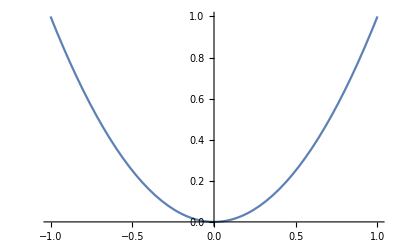

```mathematica
intervalfunctest[x^2 , x ∈ Interval[{-1,1}]]
```

```mathematica
intervalfunctest[x^2 + y^2, {x,y} ∈ Disk[]]
```

-Graphics3D-

```mathematica
intervalfunctest[{x, y} ∈ Rectangle[{-5,-5},{5,5}]]
intervalfunctest[x ∈ Interval[{-1, 1}]]
```

{{x,y},Rectangle[{-5,-5},{5,5}]}

{x,Interval[{-1,1}]}

```mathematica
PlotWavefunction[
	(thing[#1, #2,  0.4]&), { -3,3}, { -3,3},
	PlotRange -> {0, .6},
	Potential -> (#1^2/8+#2^2/8 &)
]
```

-Graphics3D-

```mathematica
Animate[
	PlotWavefunction[
		(thing[#1, #2,  t]&), { -3,3}, { -3,3},
		ShowBar -> False,
		PlotRange -> {0, .6},
		Potential -> (#1^2/8+#2^2/8 &)
	],
	{t, 0, 1}
]
```